```mathematica
(*Task A-9*)
```

```mathematica
m=({{-2., 7, 3}, {0, -3, 5}, {5, 1, -4}});
n=({{3, -2}, {1, 0}, {-4, 5}});
```

```mathematica
(*a*)
Det[m]
```

206.

```mathematica
(*b*)
Inverse[m]//MatrixForm
```

(0.0339806 | 0.150485 | 0.213592
0.121359 | -0.0339806 | 0.0485437
0.0728155 | 0.179612 | 0.0291262)

```mathematica
(*c*)
r=m.n//MatrixForm
```

(-11. | 19.
-23. | 25.
32. | -30.)

```mathematica
(*d*)
CharacteristicPolynomial[m,x]
```

206.-6. x-9. x^2-x^3

```mathematica
(*e*)
Eigenvectors[m]
```

{{0.201688-0.518827 ⅈ,0.398023+0.431619 ⅈ,-0.587727+0. ⅈ},{0.201688+0.518827 ⅈ,0.398023-0.431619 ⅈ,-0.587727+0. ⅈ},{0.750331+0. ⅈ,0.392127+0. ⅈ,0.532202+0. ⅈ}}

```mathematica
(*Task B-3*)
```

```mathematica
h[x_]:=3 x^2-5 x+Log[x]-1;
```

```mathematica
(*a*)
h'[x]
```

-5+1/x+6 x

```mathematica
D[h[x],{x,4}]
```

-6/x^4

```mathematica
(*b*)
h[√2]
```

5-5 √2+Log[2]/2

```mathematica
h'[π/4]
```

-5+4/π+(3 π)/2

```mathematica
(*c*)
Series[h[x],{x,3,4}]
```

(11+Log[3])+(40 (x-3))/3+53/18 (x-3)^2+1/81 (x-3)^3-1/324 (x-3)^4+O[x-3]^5

```mathematica
Normal[Series[h[x],{x,3,4}]]
```

11+40/3 (-3+x)+53/18 (-3+x)^2+1/81 (-3+x)^3-1/324 (-3+x)^4+Log[3]

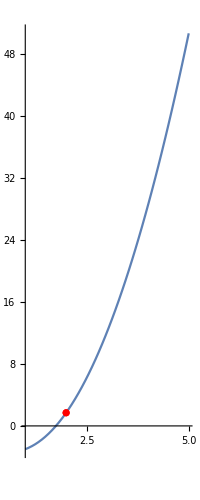

```mathematica
(*d*)
Show[Plot[h[x],{x,1,5}],ListPlot[{{2,h[2]}},PlotStyle->Red],PlotRange->All,AspectRatio->Full]
```